```mathematica
Needs["VariationalMethods`"]
```

## Task 2 : Heat conduction problem

#### 2.1 Check for the variational problem

```mathematica
F[u_]:= k/2 D[u,{{x,y}}] . D[u,{{x,y}}]
```

```mathematica
G[u_]:= u f[x,y]
```

```mathematica
phi[u_]:=Integrate[F[u],{x,-1,1},{y,-1,1}] - Integrate[G[u],{x,-1,1},{x,-1,1}]
```

```mathematica
phin[u_]:=NIntegrate[F[u],{x,-1,1},{y,-1,1}] -  NIntegrate[G[u],{x,-1,1},{x,-1,1}]
```

```mathematica
EulerEquations[F[u[x,y]]-G[u[x,y]],u[x,y],{x,y}]//FullSimplify//TraditionalForm
```

f(x,y)+k (u^(0,2)(x,y)+u^(2,0)(x,y))==0

#### 2.2 Set up bilinear form and linear form

```mathematica
k=1;f[x_,y_]:=3;
```

```mathematica
u[x_,y_]:=3x^2+5y^3
```

```mathematica
a[u_,v_]:=Integrate[k  D[u,{{x,y}}] . D[v,{{x,y}}],{x,-1,1},{y,-1,1}]
```

```mathematica
b[v_]:=Integrate[v f[x,y],{x,-1,1},{y,-1,1}]
```

```mathematica
Print["a(u,u) = ",a[u[x,y],u[x,y]]]
```

a(u,u) = 228

```mathematica
Print["b(u) = ",b[u[x,y]]]
```

b(u) = 12

#### 2.3 Establish residual function and norm

```mathematica
r[u_]:=k (D[u,{x,2}] + D[u,{y,2}]) +f[x,y]
```

```mathematica
normr[u_]:=Sqrt[Integrate[r[u]^2,{x,-1,1},{y,-1,1}]]
```

```mathematica
Print["r(x,y) = ",r[u[x,y]]]
```

r(x,y) = 9+30 y

```mathematica
Print["L2-norm-of-r = ",normr[u[x,y]]]
```

L2-norm-of-r = 2 √381

#### 2.4 Add two basis functions and plot

```mathematica
(* Trigonometric functions *)
```

```mathematica
basisT[n_]:= Table[Sin[(2i-1)(x+1)Pi/2] Sin[(2j-1)(y+1)Pi/2],{i,1,n},{j,1,n}]//Flatten
```

```mathematica
(* Legendre polynomials *)
```

```mathematica
nj[j_,x_]:=1/Sqrt[2(2j+1)] (LegendreP[j+1,x] - LegendreP[j-1,x])
```

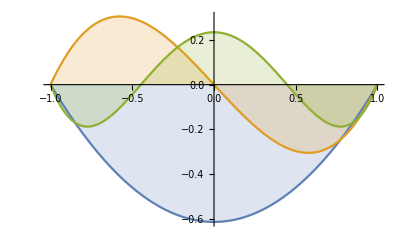

```mathematica
Plot[Evaluate[Table[nj[i,x],{i,1,3}]],{x,-1,1},PlotRange->All,Filling->Axis]
```

```mathematica
(* Polynomial functions *)
```

```mathematica
basisP[n_]:=Table[nj[2i-1,x]  nj[2j-1,y],{i,1,n},{j,1,n}]//Flatten//Simplify
```

```mathematica
Plot3D[#,{x,-1,1},{y,-1,1},SphericalRegion->True,PlotRange->All]&/@basisT[3]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Plot3D[#,{x,-1,1},{y,-1,1},SphericalRegion->True,PlotRange->All]&/@basisP[3]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

#### 2.5 Establish functions to compute solutions

##### 2.5a-----2.5b----2.5c

```mathematica
un[basis_]:=Module[{n,stiffMa,rhsMa,uh},
n=Dimensions[basis][[1]];
stiffMa=Table[a[basis[[i]],basis[[j]]],{i,1,n},{j,1,n}];
rhsMa=Table[b[basis[[i]]],{i,1,n}];
uh=LinearSolve[stiffMa,rhsMa];
Sum[uh[[i]] basis[[i]],{i,1,n}]//Simplify//N
]
```

```mathematica
(* Solutions with basis T *)
```

#### 2.6 Plot , norm and residual

```mathematica
unT=Table[un[basisT[i]],{i,1,3}];
Table[Plot3D[unT[[i]],{x,-1,1},{y,-1,1}],{i,1,Dimensions[unT][[1]]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(* Solutions with basis P *)
```

```mathematica
unP=Table[un[basisP[i]],{i,1,3}];
Table[Plot3D[unP[[i]],{x,-1,1},{y,-1,1}],{i,1,Dimensions[unP][[1]]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
r[u_]:=k (D[u,{x,2}] + D[u,{y,2}]) +f[x,y]
```

```mathematica
normr[u_]:=Sqrt[Integrate[r[u]^2,{x,-1,1},{y,-1,1}]]
```

```mathematica
Print["r(x,y) = ",FullSimplify[r[unP]]]
```

r(x,y) = {-0.75+1.875 x^2+1.875 y^2,-0.046875+0.539063 y^2-0.492188 y^4+x^4 (-0.492188+4.42969 y^2)+x^2 (0.539063-5.90625 y^2+4.42969 y^4),-0.00435913+0.157426 y^2-0.429363 y^4+0.187007 y^6+x^6 (0.187007-8.45801 y^2+18.3257 y^4)+x^2 (0.157426-5.32322 y^2+15.5261 y^4-8.45801 y^6)+x^4 (-0.429363+15.5261 y^2-42.2901 y^4+18.3257 y^6)}

```mathematica
Print["L2-norm-of-r = ",normr[unP]]
```

L2-norm-of-r = {1.87083,0.538516,0.268041}

```mathematica
Print["r(x,y) = ",FullSimplify[r[unT]]]
```

r(x,y) = {3-4.86342 Cos[1.5708 x] Cos[1.5708 y],3.+Cos[1.5708 x] (-4.86342 Cos[1.5708 y]-1.62114 Sin[4.71239 (1.+y)])+Sin[4.71239 (1.+x)] (-1.62114 Cos[1.5708 y]-0.54038 Sin[4.71239 (1.+y)]),3.+Cos[1.5708 x] (-4.86342 Cos[1.5708 y]-0.972683 Cos[7.85398 y]-1.62114 Sin[4.71239 (1.+y)])+Sin[4.71239 (1.+x)] (-1.62114 Cos[1.5708 y]-0.324228 Cos[7.85398 y]-0.54038 Sin[4.71239 (1.+y)])+Cos[7.85398 x] (-0.972683 Cos[1.5708 y]-0.194537 Cos[7.85398 y]-0.324228 Sin[4.71239 (1.+y)])}

```mathematica
Print["L2-norm-of-r = ",normr[unT]]
```

L2-norm-of-r = {3.51385,2.60749,2.15839}